```mathematica
(*PSO 20 particles, 100 iterations*)
data1={0.3310999999999999,0.33109999999999984,0.33109999999999984,0.3311000000000235,0.3311000000003633,0.33110000000772666,0.3311000000000046,0.3311000000050604,0.3311000000003207,0.33110000000000916,0.33110000000001394,0.33110000000000456,0.33110000000376394,0.3311000000159755,0.33110000000032175};
```

```mathematica
{Mean[data1],Median[data2],Median[data3]}
```

{0.3311,0.3311,0.3311}

```mathematica
(*PSO 20 particles, 500 iterations*)
data2 = {0.33109999999999984,0.3310999999999999,0.33109999999999984,0.33109999999999984,0.3310999999999998,0.3310999999999999,0.33109999999999984,0.33109999999999984,0.3310999999999998,0.3310999999999999,0.3311,0.33109999999999984,0.33109999999999984,0.33109999999999984,0.3311000000000085};
```

```mathematica
StandardDeviation[data1]
```

4.47073×10^-12

```mathematica
StandardDeviation[data2]
```

2.2328×10^-15

```mathematica
StandardDeviation[data1](*StdDev for 20np 100nit*)
```

4.47073×10^-12

```mathematica
StandardDeviation[data2](*StdDev for 20np 500nit*)
```

2.60506×10^-15

```mathematica
(*PSO 40 particles, 100 iterations*)data3 = {0.3311000000024352,0.33110000001074713,0.3311000000000046,0.33110000000082634,0.3311000000002402,0.3311000000001075,0.33110000022497593,0.3311000000000255,0.3310999999999999,0.3310999999999999,0.3311};
```

```mathematica
StandardDeviation[data3](*StdDev for 40np 100nit*)
```

6.74743×10^-11

```mathematica
data4=Flatten[Import["~/Desktop/Uni\ shizz\ 4th\ year/CS4525\ Project/Haskell/ghc-eden-7.6.1/testing2.txt","Data"]]

Sort[{0.3310999999999999,0.33109999999999984,0.33109999999999984,0.3311000000000235,0.3311000000003633,0.33110000000772666,0.3311000000000046,0.3311000000050604,0.3311000000003207,0.33110000000000916,0.33110000000001394,0.33110000000000456,0.33110000000376394,0.3311000000159755,0.33110000000032175},Less]
```

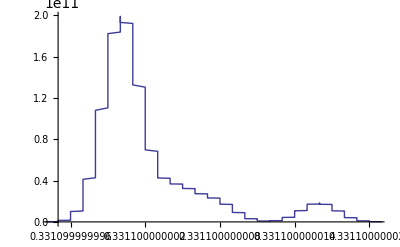

```mathematica
SmoothHistogram[data1,Automatic,"PDF"]
```

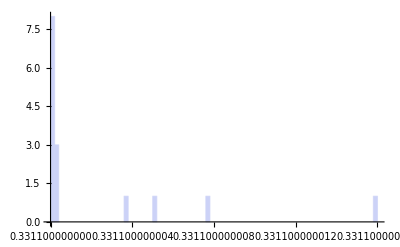

```mathematica
Histogram[data1,100]
```

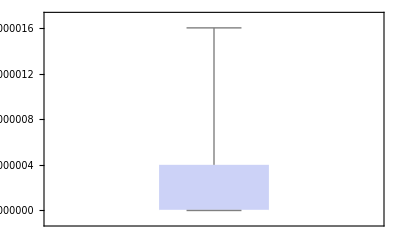

```mathematica
BoxWhiskerChart[data1]
```